Autor: Krzysztof Barczak

# Metody numeryczne w technice

## (kierunek Matematyka)

## Projekt 8

Metoda różnic skończonych

Nieustalony przepływ ciepła (schemat jawny)

Napisać procedurę realizującą schemat jawny metody różnic skończonych dla zagadnienia nieustalonego przepływu ciepła:

c ρ (∂u)/(∂t)=λ (∂^2 u)/(∂x^2),   x∈(a,b),  t∈(0,t^*),

z warunkiem początkowym:

u(x,0) = u_0(x),

oraz warunkami brzegowymi pierwszego rodzaju:

u(a,t)=u_a(t),
u(b,t)=u_b(t).

Jako argument procedury należy podać liczbę nx węzłów siatki oraz czas końca t^*, natomiast krok czasu dt należy wyznaczyć (w programie) tak aby zapewnić stabilność obliczeń.

a) Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia, w którym:

a=1, b=2,  t^*=1, 
c=1,  ρ=1, λ=1,

u_0(x)=x^3/6,
u_a(t)=t+1/6,
u_b(t)=2t+4/3.

Przedział [a,b] podzielić na 10 części.

Na wspólnym rysunku wykreślić rozwiązanie dokładne, którym jest funkcja u(x,t)=x^3/6+x t, oraz uzyskane rozwiązania przybliżone w chwili końcowej. Wykreślić także błędy uzyskanego rozwiązania przybliżonego w chwili końcowej.

## Rozwiązanie

### Kod procedury

```mathematica
mrsjawny[c_,ρ_,λ_,f_,a_,b_,tstar_,φ_,ψ_,u0_,nx_,u_]:=Module[{h=(b-a)/(nx-1),τ,w,PP,dt,xi,tk,fik,rozwiazanie,macierz,eq,expr,neweq,const,wskazniki,zmienne,liczbaWierszy,matrix,wyrazyWolne,solution,dummy,wykres,rozwiazanieWykres,bledy,bledyWykres,bledyWykresPlot,koncowe,bledyKoncowe,bledyKoncoweWykres},
w={τ λ,cρh^2-2λτ,-c ρ h^2,-h^2 τ};
(* Wyznaczenie kroku czasu *)
τ=(c ρ h^2)/(2 λ);
PP=Ceiling[2tstar/τ];
dt=N[tstar/(PP-1)];
(*Print["τ = ",N[τ],"; dt = ",dt,"; dt <= τ ",dt<=τ];*)

(* Wyznaczenie siatki *)
xi=Table[a+(i-1) h,{i,nx}];
tk=Table[(k-1) dt,{k,PP}];
(*Print["xi ",xi];
Print["tk ",tk];*)

(* Wartości funkcji f w węzłach siatki *)
fik=Table[f[xi[[i]],tk[[k]]],{i,nx},{k,PP}];

(* Wartości znane z warunków *)
rozwiazanie=Table[Subscript[u, i,k],{i,nx},{k,PP}];

Do[rozwiazanie[[i,1]]=u0[xi[[i]]],{i,1,nx}];
(*Print[MatrixForm[rozwiazanie]];*)

Do[rozwiazanie[[1,k]]=φ[tk[[k]]];
rozwiazanie[[nx,k]]=ψ[tk[[k]]],
{k,1,PP}];
(*Print[MatrixForm[rozwiazanie]];*)

(* Budowa układu równań *)
macierz=Table[eq=w[[1]] rozwiazanie[[i+1,k]]+w[[2]]rozwiazanie[[i,k]]+w[[3]]rozwiazanie[[i,k+1]]+w[[1]]rozwiazanie[[i-1,k]]==w[[4]] fik⟦i,k⟧;
expr=eq/.Equal->Subtract;
const=expr/.Map[#->0&,Variables[expr]];neweq=expr-const==-const,{i,2,nx-1},{k,1,PP-1}];
macierz=Flatten[macierz];
(*Print[MatrixForm[macierz]];*)

(*Print["n = ",nx+1,", m = ",PP+1,", nm - n - 2m + 2 = ",(nx+1)( PP+1)-(nx+1)-2(PP+1)+2];
Print[Dimensions[macierz]];*)

wskazniki=Sort[DeleteDuplicates[Flatten[Table[{{i+1,k},{i,k},{i,k+1},{i-1,k}},{i,2,nx-1},{k,2,PP-1}],2]]];
zmienne=Sort[DeleteDuplicates[Flatten[Table[{Subscript[u, i+1,k],Subscript[u, i,k],Subscript[u, i,k+1],Subscript[u, i-1,k]},{i,2,nx-1},{k,2,PP-1}],2]]];
(*Print["wskazniki ",wskazniki];*)

liczbaWierszy=Dimensions[macierz][[1]];
(*Print["liczba wierszy ",liczbaWierszy];*)

(* Rozdzielenie zmiennych od wyrazów wolnych *)
matrix=Table[0,{nx PP-nx-2PP+2}];wyrazyWolne=Table[0,{nx PP-nx-2PP+2}];
Do[matrix[[i]]=macierz[[i,1]];wyrazyWolne[[i]]=macierz[[i,2]],{i,nx PP-nx-2PP+2}];

(*Print["wyrazy wolne ",MatrixForm[wyrazyWolne]];*)

(* Wyciągnięcie macierzy współczynników *)
matrix=Normal@CoefficientArrays[matrix,zmienne][[2]];
(*Print[MatrixForm[matrix]];
Print["wymiary matrix", Dimensions[matrix]];*)

(* Rozwiązanie *)
solution=LinearSolve[matrix,wyrazyWolne];
(*Print["solution ",solution];
Print["liczba roz ",Dimensions[solution]];*)

dummy=Table[0,{nx},{PP}];
Do[dummy[[i[[1]],i[[2]]]]=solution[[Position[wskazniki,i][[1,1]]]],{i,wskazniki}];
(*Print["dummy ",MatrixForm[dummy]];
Print["dim dummy ",Dimensions[dummy]];*)

Do[rozwiazanie[[i,j]]=dummy[[i,j]],{i,2,nx-1},{j,2,PP}];
(*Print[MatrixForm[rozwiazanie]];*)

(* Tworzenie wykresu *)
wykres=Table[{xi[[i]],tk[[k]],rozwiazanie[[i,k]]},{i,nx},{k,PP}];
dummy={};
Do[dummy=Append[dummy,wykres[[i,k]]],{i,nx},{k,PP}];
rozwiazanieWykres=ListPointPlot3D[dummy,PlotTheme->"Business",PlotRange->All];
koncowe={};
(*koncowe=ListPlot3D[Table[{xi[[i]],tk[[PP]],rozwiazanie[[i,PP]]},{i,nx}],PlotTheme->"Business"];*)
Do[koncowe=Append[koncowe,wykres[[i,PP]]],{i,nx}];
koncowe=ListPointPlot3D[koncowe,PlotTheme->"Business",PlotRange->All,PlotLegends->{"przybliżone dla t = t^*"}];
(*Print[koncowe];*)

(* Błędy *)
bledy=Table[{xi[[i]],tk[[k]],Abs[rozwiazanie[[i,k]]-u[xi[[i]],tk[[k]]]]},{i,nx},{k,PP}];
bledyWykres={};
Do[bledyWykres=Append[bledyWykres,bledy[[i,k]]],{i,nx},{k,PP}];
bledyWykresPlot=ListPlot3D[bledyWykres,PlotTheme->"Business",PlotStyle->96];

bledyKoncowe=Table[{xi[[i]],Abs[rozwiazanie[[i,PP]]-u[xi[[i]],tk[[PP]]]]},{i,nx}];
bledyKoncoweWykres={};
Do[bledyKoncoweWykres=Append[bledyKoncoweWykres,bledyKoncowe[[i]]],{i,nx}];
bledyKoncoweWykres=ListPlot[bledyKoncoweWykres,PlotTheme->"Business",Joined->True];

Return[{Show[Plot3D[u[x,t],{x,a,b},{t,0,tstar},PlotStyle->Green,PlotLegends->{"dokładne"}],koncowe],bledyKoncoweWykres}]
]
```

### Rozwiązanie

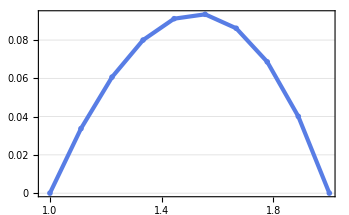
{-Graphics3D-,-Graphics-}

```mathematica
Clear[c,ρ,λ,f,a,b,tstar,φ,ψ,u0,nx,u];
c=1;ρ=1;λ=1;f[x_,t_]:=0;a=1;b=2;tstar=1;
φ[t_]:=t+1/6;ψ[t_]:=2t+4/3;u0[x_]:=x^3/6;
u[x_,t_]:=x^3/6+x t;
nx=10;
mrsjawny[c,ρ,λ,f,a,b,tstar,φ,ψ,u0,nx,u]
```